-0.00625959

1.30867

-0.0207654

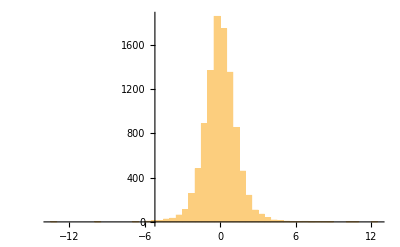

```mathematica
(*生成StudentT分布的随机数据*)dataT=RandomVariate[StudentTDistribution[5],1000];
(*数据分析：例如，计算均值、标准差和中位数*)
Mean[dataT]
StandardDeviation[dataT]
Median[dataT]
(*绘制直方图*)
Histogram[dataT,PlotRange->{{-5,5},{0,All}}]
```

-0.889946

25.1769

-0.0635611

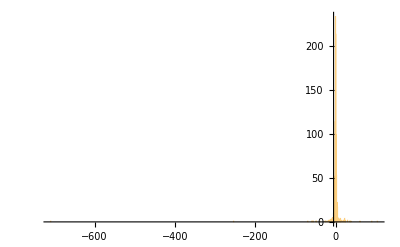

```mathematica
(*生成Cauchy分布的随机数据*)dataC=RandomVariate[CauchyDistribution[0,1],1000];
(*数据分析：例如，计算均值、标准差和中位数*)
Mean[dataC]
StandardDeviation[dataC]
Median[dataC]
(*绘制直方图*)
Histogram[dataC,PlotRange->{{-5,5},{0,All}}]
```

1.27416

0.646813

1.22797

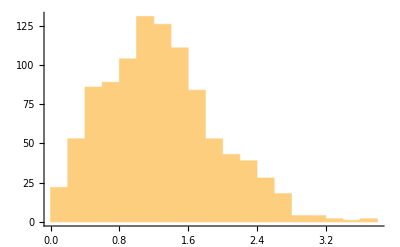

```mathematica
(*生成Rayleigh分布的随机数据*)dataR=RandomVariate[RayleighDistribution[1],1000];
(*数据分析：例如，计算均值、标准差和中位数*)
Mean[dataR]
StandardDeviation[dataR]
Median[dataR]
(*绘制直方图*)
Histogram[dataR,PlotRange->{{0,4},{0,All}}]
```

2989/1000

(91 √(359/1110))/30

3

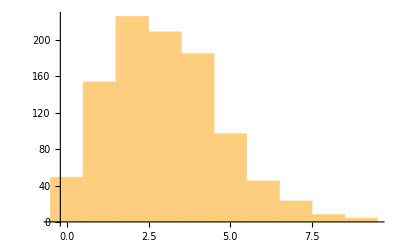

```mathematica
(*生成Poisson分布的随机数据*)dataP=RandomVariate[PoissonDistribution[3],1000];
(*数据分析：例如，计算均值、标准差和中位数*)
Mean[dataP]
StandardDeviation[dataP]
Median[dataP]
(*绘制直方图*)
Histogram[dataP,PlotRange->{{0,10},{0,All}}]
```

5073/1000

(√(2669671/1110))/30

5

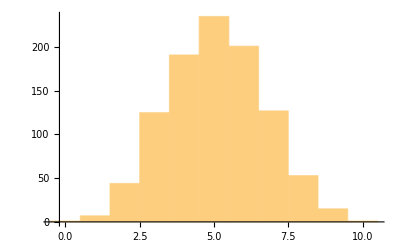

```mathematica
(*生成Binomial分布的随机数据*)dataB=RandomVariate[BinomialDistribution[10,0.5],1000];
(*数据分析：例如，计算均值、标准差和中位数*)
Mean[dataB]
StandardDeviation[dataB]
Median[dataB]
(*绘制直方图*)
Histogram[dataB,PlotRange->{{0,10},{0,All}}]
```

```mathematica
list=Range[13]
shuffleList[listx_]:=Module[{list=listx,n=Length[listx],temp,i},
For[i=n,i>1,i--,
j=RandomInteger[{1,i}];
(*交换i和j位置对应的数值*)
temp=list[[i]];
list[[i]]=list[[j]];
list[[j]]=temp;
];
Return[list];
]

randomSample=RandomSample[list,13]
shuffledList=shuffleList[list]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13}

{1,6,7,9,4,2,11,5,12,3,10,8,13}

{4,9,1,7,5,6,10,2,3,12,13,11,8}